```mathematica
SetDirectory[NotebookDirectory[]];
```

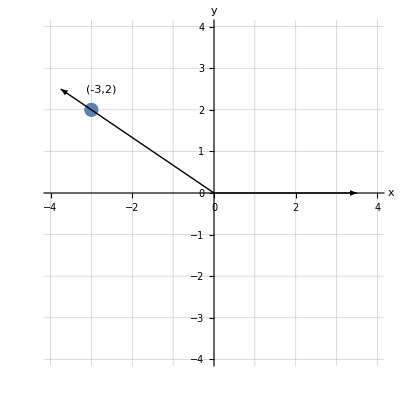

{trigfunctionexample-1.pdf,trigfunctionexample-1.svg}

```mathematica
Show[
ListPlot[{{-3,2}},PlotStyle->PointSize[0.025]],
Graphics[Arrow[{{0,0},1.25{-3,2}}]],
Graphics[Arrow[{{0,0},3.5{1,0}}]],
AxesLabel->{HoldForm[x],HoldForm[y]},
AxesStyle->Directive[16],
GridLines->{Range[-4,4],Range[-4,4]},
PlotRange->{{-4,4},{-4,4}},
AspectRatio->1,
Epilog->{Style[Text["(-3,2)",{-3+0.25,2.5}],16]}
]
Export[{"trigfunctionexample-1.pdf","trigfunctionexample-1.svg"},%]
```

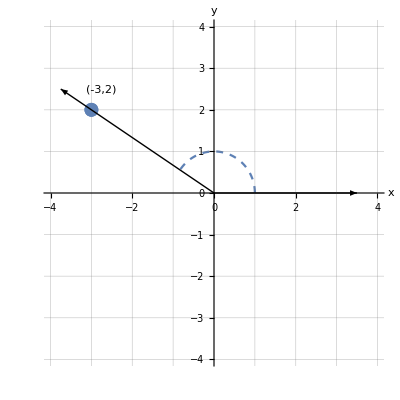

{trigfunctionexample-1-2.pdf,trigfunctionexample-1-2.svg}

```mathematica
Show[
ListPlot[{{-3,2}},PlotStyle->PointSize[0.025]],
ParametricPlot[{Cos[t],Sin[t]},{t,0,ArcTan[-2/3]+Pi},PlotStyle->Dashed],
Graphics[Arrow[{{0,0},1.25{-3,2}}]],
Graphics[Arrow[{{0,0},3.5{1,0}}]],
AxesLabel->{HoldForm[x],HoldForm[y]},
AxesStyle->Directive[16],
GridLines->{Range[-4,4],Range[-4,4]},
PlotRange->{{-4,4},{-4,4}},
AspectRatio->1,
Epilog->{Style[Text["(-3,2)",{-3+0.25,2.5}],16]}
]
Export[{"trigfunctionexample-1-2.pdf","trigfunctionexample-1-2.svg"},%]
```

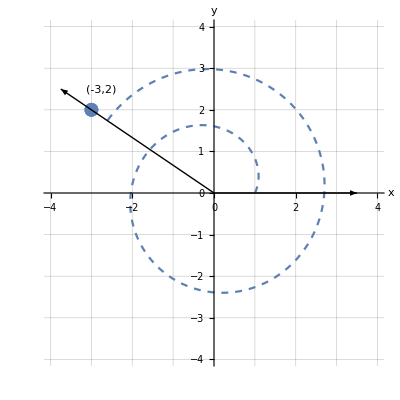

{trigfunctionexample-1-3.pdf,trigfunctionexample-1-3.svg}

```mathematica
Show[
ListPlot[{{-3,2}},PlotStyle->PointSize[0.025]],
ParametricPlot[{Sqrt[t+1]Cos[t],Sqrt[t+1]Sin[t]},{t,0,ArcTan[-2/3]+Pi+2Pi},PlotStyle->Dashed],
Graphics[Arrow[{{0,0},1.25{-3,2}}]],
Graphics[Arrow[{{0,0},3.5{1,0}}]],
AxesLabel->{HoldForm[x],HoldForm[y]},
AxesStyle->Directive[16],
GridLines->{Range[-4,4],Range[-4,4]},
PlotRange->{{-4,4},{-4,4}},
AspectRatio->1,
Epilog->{Style[Text["(-3,2)",{-3+0.25,2.5}],16]}
]
Export[{"trigfunctionexample-1-3.pdf","trigfunctionexample-1-3.svg"},%]
```

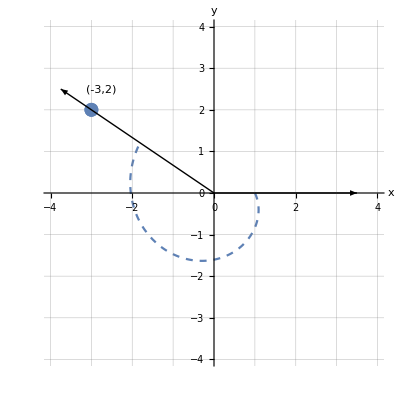

{trigfunctionexample-1-4.pdf,trigfunctionexample-1-4.svg}

```mathematica
Show[
ListPlot[{{-3,2}},PlotStyle->PointSize[0.025]],
ParametricPlot[{Sqrt[t+1]Cos[-t],Sqrt[t+1]Sin[-t]},{t,0,ArcTan[2/3]+Pi},PlotStyle->Dashed],
Graphics[Arrow[{{0,0},1.25{-3,2}}]],
Graphics[Arrow[{{0,0},3.5{1,0}}]],
AxesLabel->{HoldForm[x],HoldForm[y]},
AxesStyle->Directive[16],
GridLines->{Range[-4,4],Range[-4,4]},
PlotRange->{{-4,4},{-4,4}},
AspectRatio->1,
Epilog->{Style[Text["(-3,2)",{-3+0.25,2.5}],16]}
]
Export[{"trigfunctionexample-1-4.pdf","trigfunctionexample-1-4.svg"},%]
```

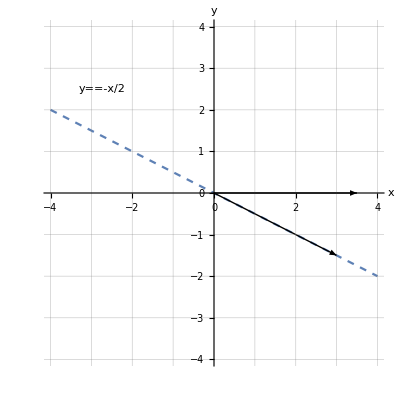

{trigfunctionexample-2.pdf,trigfunctionexample-2.svg}

```mathematica
Show[
Plot[{-x/2},{x,-4,4},PlotStyle->Dashed],
(*ListPlot[{{-3,2}},PlotStyle->PointSize[0.025]],
*)
(*Graphics[Arrow[{{0,0},1.25{-3,2}}]],*)
Graphics[Arrow[{{0,0},3.5{1,0}}]],
Graphics[Arrow[{{0,0},1.5{2,-1}}]],
AxesLabel->{HoldForm[x],HoldForm[y]},
AxesStyle->Directive[16],
GridLines->{Range[-4,4],Range[-4,4]},
PlotRange->{{-4,4},{-4,4}},
AspectRatio->1,
Epilog->{Style[Text[HoldForm[y==-x/2],{-3+0.25,2.5}],16]}
(*Epilog->{Style[Text["(-3,2)",{-3+0.25,2.5}],16]}*)
]
Export[{"trigfunctionexample-2.pdf","trigfunctionexample-2.svg"},%]
```

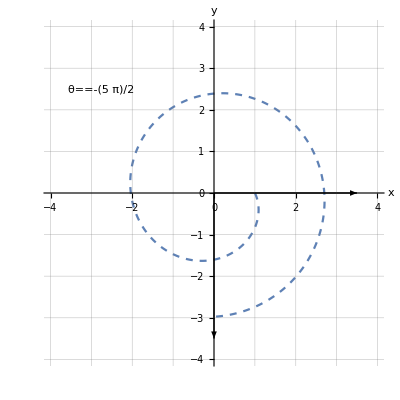

{trigfunctionexample-3.pdf,trigfunctionexample-3.svg}

```mathematica
Show[
ParametricPlot[{Sqrt[t+1]Cos[-t],Sqrt[t+1]Sin[-t]},{t,0,5Pi/2},PlotStyle->Dashed],
(*ListPlot[{{-3,2}},PlotStyle->PointSize[0.025]],
*)
(*Graphics[Arrow[{{0,0},1.25{-3,2}}]],*)
Graphics[Arrow[{{0,0},3.5{1,0}}]],
Graphics[Arrow[{{0,0},3.5{0,-1}}]],
AxesLabel->{HoldForm[x],HoldForm[y]},
AxesStyle->Directive[16],
GridLines->{Range[-4,4],Range[-4,4]},
PlotRange->{{-4,4},{-4,4}},
AspectRatio->1,
Epilog->{Style[Text[HoldForm[θ==-5Pi/2],{-3+0.25,2.5}],16]}
(*Epilog->{Style[Text["(-3,2)",{-3+0.25,2.5}],16]}*)
]
Export[{"trigfunctionexample-3.pdf","trigfunctionexample-3.svg"},%]
```